# Fitting the binding curve

## Reading the data

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[], "2023.02.21.13.19.23"}]];
```

```mathematica
distances=BinaryReadList["distances.dat","Real32"];
angles=BinaryReadList["angles.dat","Real32"];
bindingEnergies=ArrayReshape[BinaryReadList["binding_energies.dat","Real32"],{Length[angles], Length[distances]}];
startingDistance={1, 1, 2,3,5,7,8,10,12,15,18,24,27,24,17,17,16,21,25,24};
morseFitQuality=BinaryReadList["morse_fit_quality.dat","Real32"];
morseFitScatter=Join[{Table[{angles[[i+1]],morseFitQuality[[i]]},{i,1,14}],{{angles[[18]],morseFitQuality[[17]]},{angles[[19]],morseFitQuality[[18]]}}}]//Flatten[#,1]&;
entropy=ArrayReshape[BinaryReadList["entropies.dat","Real32"],{Length[angles], Length[distances]}];
```

## Morse potential (works well, in the paper)

## Morse potential fit

```mathematica
Do[
start=startingDistance[[angleIDX-1]];
scatter=Table[{distances[[i]],bindingEnergies[[angleIDX,i]]},{i,start,Length[distances]-start}];
nlm=Normal[NonlinearModelFit[scatter,De(Exp[-2a(r-re)]-2Exp[-a(r-re)]),{De,a,re},r,MaxIterations->∞]];
Print[FortranForm[nlm]];
,{angleIDX,2,20}]
```

5.580390309448237*(E**(-3.0377471897088193*(-0.528669782788294 + r)) - 2/E**(1.5188735948544096*(-0.528669782788294 + r)))

3.4274486627573997*(E**(-3.799380158605931*(-0.47973290114432926 + r)) - 2/E**(1.8996900793029654*(-0.47973290114432926 + r)))

2.285401169096024*(E**(-4.402463155249511*(-0.4631079255337017 + r)) - 2/E**(2.2012315776247555*(-0.4631079255337017 + r)))

1.551192171427588*(E**(-4.81570374860555*(-0.4642655447957261 + r)) - 2/E**(2.407851874302775*(-0.4642655447957261 + r)))

1.0598470742964785*(E**(-5.1410754088615755*(-0.4783898190284267 + r)) - 2/E**(2.5705377044307878*(-0.4783898190284267 + r)))

0.7148220809706628*(E**(-5.3904241278507286*(-0.5018955265663114 + r)) - 2/E**(2.6952120639253643*(-0.5018955265663114 + r)))

0.46331721539795195*(E**(-5.5069105743552305*(-0.5384565406606292 + r)) - 2/E**(2.7534552871776152*(-0.5384565406606292 + r)))

0.28495211368558043*(E**(-5.501660360933069*(-0.5868720195028256 + r)) - 2/E**(2.7508301804665347*(-0.5868720195028256 + r)))

0.16054553861792828*(E**(-5.406762370032314*(-0.6589019567964931 + r)) - 2/E**(2.703381185016157*(-0.6589019567964931 + r)))

0.0802423625900907*(E**(-5.2807411035440905*(-0.7610680973692473 + r)) - 2/E**(2.6403705517720453*(-0.7610680973692473 + r)))

0.031941895762222915*(E**(-4.8881023079372845*(-0.9318352120398004 + r)) - 2/E**(2.4440511539686423*(-0.9318352120398004 + r)))

-0.21795992863678978*(E**(-18.93357243882598*(-0.419031099683263 + r)) - 2/E**(9.46678621941299*(-0.419031099683263 + r)))

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

-4.596185038513766e8*(E**(-11.486738219445648*(3.3611808687392295 + r)) - 2/E**(5.743369109722824*(3.3611808687392295 + r)))

-8.435877205314344e8*(E**(-9.835982910255005*(4.090374604186538 + r)) - 2/E**(4.917991455127503*(4.090374604186538 + r)))

-5595.4996148289965*(-2*E**(3.473725867625206e-6*(199537.59265461436 + r)) + E**(6.947451735250412e-6*(199537.59265461436 + r)))

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

-6257.5024012085705*(-2*E**(3.613860552846493e-6*(191800.01322388317 + r)) + E**(7.227721105692986e-6*(191800.01322388317 + r)))

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

-8.295441352250288e8*(E**(-7.322600983736511*(5.601532048938182 + r)) - 2/E**(3.6613004918682557*(5.601532048938182 + r)))

-6.724554904237205e8*(E**(-6.6512902613294616*(6.16433364343066 + r)) - 2/E**(3.3256451306647308*(6.16433364343066 + r)))

-6.93498780797546e8*(E**(-6.731259579708323*(6.08636414436295 + r)) - 2/E**(3.3656297898541614*(6.08636414436295 + r)))

```mathematica
angleIDX=14;
startingDistance=18;
scatter=Table[{distances[[i]],bindingEnergies[[angleIDX,i]]},{i,startingDistance,Length[distances]-startingDistance}];
```

```mathematica
nlm=Normal[NonlinearModelFit[scatter,De(Exp[-2a(r-re)]-2Exp[-a(r-re)]),{De,a,re},r]]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-39.5349 (ⅇ^(-11.5002 (0.527145+r))-2 ⅇ^(-5.75012 (0.527145+r)))

```mathematica
nlm=Normal[NonlinearModelFit[scatter,De(Exp[-a r]),{De,a},r]]
```

1.76114 ⅇ^(-3.36563 r)

```mathematica
nlm=Normal[NonlinearModelFit[scatter,4ϵ((σ/r)^12-(σ/r)^6),{ϵ,σ},r]]
```

1.50477 ((2.08395×10^-7)/r^12-0.000456503/r^6)

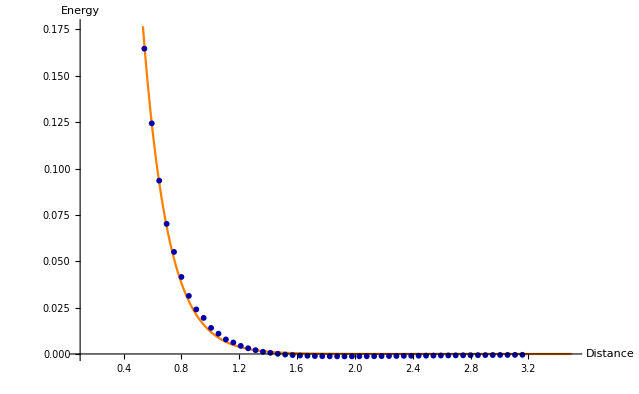

```mathematica
Clear[f]
f[r_]:=-39.53491142497741 (ⅇ^(-11.50023858598874 (0.5271449727957873+r))-2 ⅇ^(-5.75011929299437 (0.5271449727957873+r)))
Show[Plot[f[x],{x,0.1,3.5},PlotStyle->{Orange},AxesLabel ->{Distance,Energy}],ListPlot[scatter[[;; ;; 3]],PlotMarkers->{Automatic,6},PlotStyle->Darker[Blue]]]
```

```mathematica
FortranForm[0.46162512831719266 (ⅇ^(-5.473740049665798 (-0.5382686719819294+r))-2 ⅇ^(-2.736870024832899 (-0.5382686719819294+r)))]
```

0.46162512831719266*(E**(-5.473740049665798*(-0.5382686719819294 + r)) - 
     -    2/E**(2.736870024832899*(-0.5382686719819294 + r)))

## Fit of the fit

```mathematica
nlm=Normal[NonlinearModelFit[morseFitScatter,De(Exp[-a r]),{De,a},r]]//FortranForm
```

0.7562780555949897/E**(7.90810731120047*r)

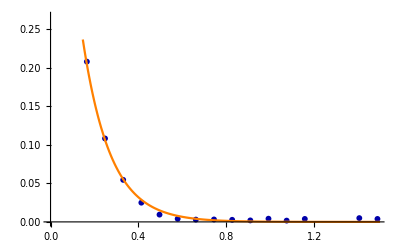

```mathematica
Clear[f]
f[r_]:=0.7562780555949897 ⅇ^(-7.90810731120047 r)
Show[ListPlot[morseFitScatter,PlotMarkers->{Automatic,6},PlotStyle->Darker[Blue]],Plot[f[x],{x,0.001,1.5},PlotStyle->{Orange},AxesLabel ->{Distance,Energy}]]
```

```mathematica
f[r]//FortranForm
```

10.698201438598309/E**(7.941329322829148*r)

## Exponential + polynomial fit (doesn’t work well)

## exp + poly fit

51584.71182740528/E**(54.68505675469281*x) - 0.00021786945630608494/x**6

30719.729404211485/E**(46.63308174034488*x) - 0.00033708611981152556/x**6

20972.415853339004/E**(40.600350785337234*x) - 0.0005265864999699283/x**6

16238.015454545633/E**(32.49623235015713*x) - 0.0015619841410711467/x**6

12049.001826246737/E**(27.069213198758856*x) - 0.003481504642362716/x**6

8448.539131221192/E**(24.674491090007034*x) - 0.004219896780031862/x**6

5532.297425375119/E**(21.537846252806816*x) - 0.00625567569023547/x**6

3467.6891365286547/E**(18.979792852142896*x) - 0.008343412572941352/x**6

1998.0805408174817/E**(16.139178534245733*x) - 0.012672324813822466/x**6

990.5641995761171/E**(13.946537278615889*x) - 0.01480369898283506/x**6

401.79898494139377/E**(11.09434388194715*x) - 0.02328374153562985/x**6

77.69109802853032/E**(9.246105198043246*x) - 0.01049427788440174/x**6

66.75013665313433/E**(8.774045532326276*x) - 0.009907093482116125/x**6

3.100869177168573/E**(4.92066017492597*x) - 1.28229152470301e-6/x**6

284.8494807807726/E**(11.649033159316573*x) - 0.008758594611546905/x**6

475.5119106056497/E**(12.61829137336114*x) - 0.009804991100239276/x**6

306.6404171159651/E**(10.173418840813857*x) - 0.02299984313586268/x**6

126.01880754988716/E**(8.269001166569257*x) - 0.028229558457776992/x**6

241.65205772785842/E**(9.089571109286213*x) - 0.03539324376564733/x**6

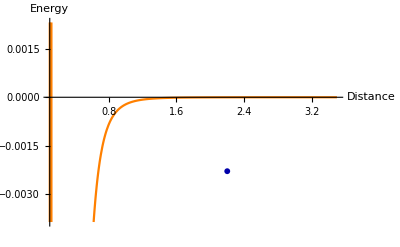
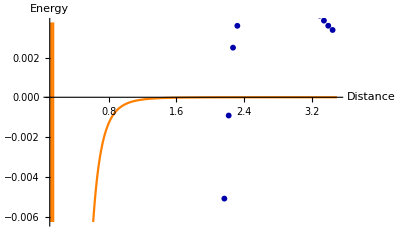
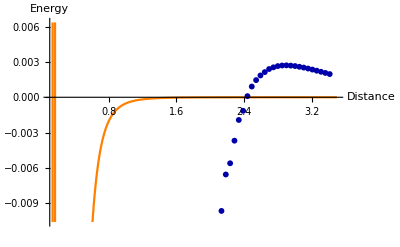
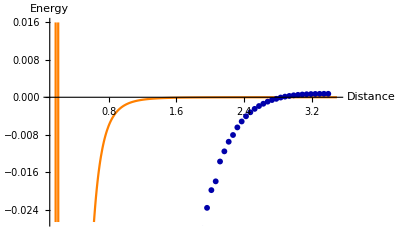
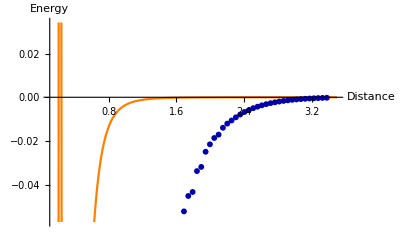
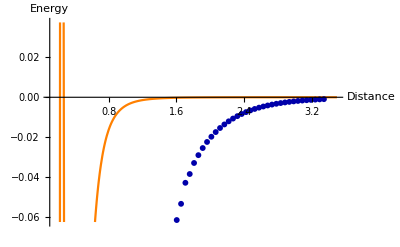
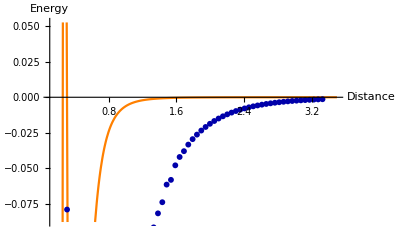
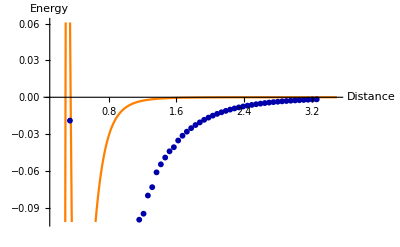
{Null,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plot={Null};
Do[
start=startingDistance[[angleIDX]];
scatter=Table[{distances[[i]],bindingEnergies[[angleIDX,i]]},{i,start,Length[distances]-start}];
f[x_]:=Normal[NonlinearModelFit[scatter,{a Exp[- b r]-c/r^6,{a>0,b>0,c>0}},{a,b,c},r]]/.r->x;
Print[FortranForm[f[x]]];
AppendTo[plot,Show[Plot[f[x],{x,0.1,3.5},PlotStyle->{Orange},AxesLabel ->{Distance,Energy}],ListPlot[scatter[[;; ;; 3]],PlotMarkers->{Automatic,6},PlotStyle->Darker[Blue]]]]
,{angleIDX,2,20}]
plot
```

## Fit of fit (to do)

```mathematica
nlm=Normal[NonlinearModelFit[morseFitScatter,De(Exp[-a r]),{De,a},r]]//FortranForm
```

0.7562780555949897/E**(7.90810731120047*r)

```mathematica
Clear[f]
f[r_]:=0.7562780555949897 ⅇ^(-7.90810731120047 r)
Show[ListPlot[morseFitScatter,PlotMarkers->{Automatic,6},PlotStyle->Darker[Blue]],Plot[f[x],{x,0.001,1.5},PlotStyle->{Orange},AxesLabel ->{Distance,Energy}]]
```

-Graphics-

```mathematica
f[r]//FortranForm
```

10.698201438598309/E**(7.941329322829148*r)

## Refined Morse potential (just experimenting)

## exp + poly fit

-1.106764880756248/E**(0.7308313917065932*x) - 5.202988432409525/E**(0.7308313878784704*x)

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

318.20509122291753/E**(2.654922897598182*x) - 314.6649195729518/E**(2.553215597107187*x)

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-1.1895653735899363/E**(0.9838391220075435*x) - 1.3323439296319748/E**(0.9838391209638386*x)

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

161.98270064271884/E**(3.3882938011878285*x) - 157.6941423550602/E**(3.233609259268954*x)

73.43933697037126/E**(3.687551431915726*x) - 69.09915533083928/E**(3.3918123379511194*x)

21.23848523956467/E**(4.249635248146038*x) - 16.78214427253391/E**(3.282950605208233*x)

8.81600974253516/E**(5.646845458185613*x) - 3.786653486651852/E**(2.700219653159149*x)

7.0933657437501845/E**(6.411383501022104*x) - 1.876846347810239/E**(2.4384483373814057*x)

6.492130778861277/E**(7.003903703659716*x) - 0.9427535914449036/E**(2.188738463323596*x)

6.134985172879146/E**(7.253764178255839*x) - 0.4487613228934411/E**(1.9466106894887005*x)

5.829309966709704/E**(7.203358653696693*x) - 0.16269787799113242/E**(1.5925540454912077*x)

-1558.7401790409542/E**(14.124037417250497*x) + 956.8236757640087/E**(12.967318735230057*x)

2805.1001560405607/E**(25.825756209931296*x) + 2.885635271526913/E**(5.309041688353892*x)

6.042611301907215/E**(8.54464438542748*x) + 0.9930331104179051/E**(3.528061752108904*x)

4.7366819995969545/E**(6.916006299343658*x) + 0.5421167484748592/E**(2.675304170175925*x)

4.9752289807102645/E**(7.007592446275235*x) + 0.591423920548103/E**(2.535681693601427*x)

3.6601922326515117/E**(5.903569794012465*x) + 0.42262554674468905/E**(2.198746979740547*x)

3.0161495263785745/E**(5.251261401904836*x) + 0.3219400897462384/E**(1.984018033741247*x)

3.2724106835361964/E**(5.476789109088344*x) + 0.3639321692040605/E**(2.0328756666556203*x)

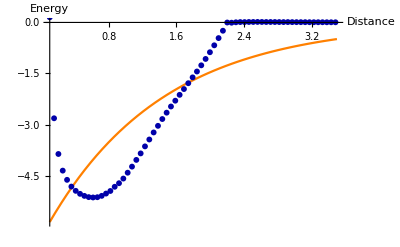
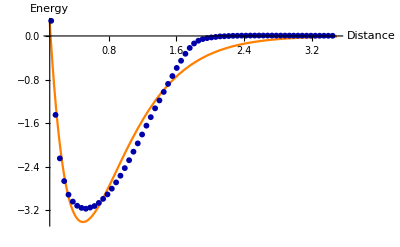
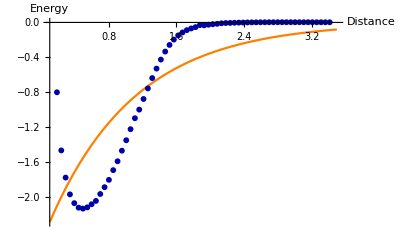
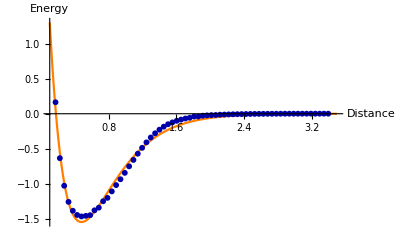
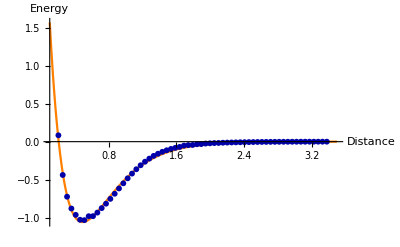
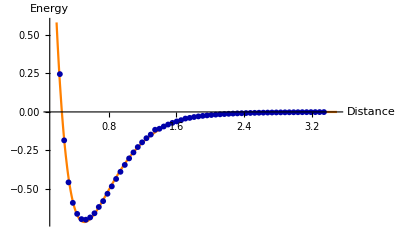
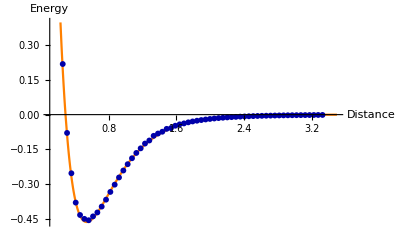
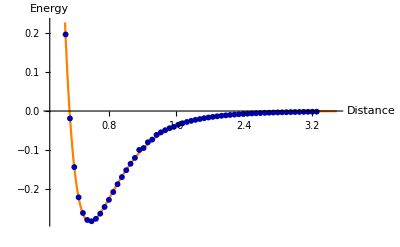
{Null,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plot={Null};
Do[
start=startingDistance[[angleIDX]];
scatter=Table[{distances[[i]],bindingEnergies[[angleIDX,i]]},{i,start,Length[distances]-start}];
f[x_]:=Normal[NonlinearModelFit[scatter,a Exp[-b r]- c Exp[-d r],{a,b,c, d},r]]/.r->x;
Print[FortranForm[f[x]]];
AppendTo[plot,Show[Plot[f[x],{x,0.1,3.5},PlotStyle->{Orange},AxesLabel ->{Distance,Energy}],ListPlot[scatter[[;; ;; 3]],PlotMarkers->{Automatic,6},PlotStyle->Darker[Blue]]]]
,{angleIDX,2,20}]
plot
```

## Lennard-Jones potential (doesn’t work well)

## Lennard-Jones potential fit

```mathematica
g[r_]:=4ϵ((σ/r)^12-(σ/r)^6)
Solve[D[g[r],r]==0,r]
```

{{r→-2^(1/6) σ},{r→2^(1/6) σ},{r→-(-1)^(1/3) 2^(1/6) σ},{r→(-1)^(1/3) 2^(1/6) σ},{r→-(-1)^(2/3) 2^(1/6) σ},{r→(-1)^(2/3) 2^(1/6) σ}}

```mathematica
g[2^(1/6) σ]
```

-ϵ

```mathematica
Do[
start=startingDistance[[angleIDX-1]];
scatter=Table[{distances[[i]],bindingEnergies[[angleIDX,i]]},{i,start,Length[distances]-start}];
nlm=Normal[NonlinearModelFit[scatter,4ϵ((σ/r)^12-(σ/r)^6),{ϵ,σ},r,MaxIterations->∞]];
Print[FortranForm[nlm]];
,{angleIDX,2,20}]
```

14.28437437638727*(1.0641815684465783e-12/r**12 - 1.031591764433285e-6/r**6)

7.452182413554963*(7.562454315873993e-12/r**12 - 2.7499916937827272e-6/r**6)

4.12815247901313*(4.523534696608139e-11/r**12 - 6.7257227839155986e-6/r**6)

3.910501246217263*(6.304074245866616e-10/r**12 - 0.00002510791557630106/r**6)

3.1627167214301064*(5.792809985250818e-9/r**12 - 0.00007611051166068205/r**6)

1.707251077383909*(1.8619201372275537e-8/r**12 - 0.00013645219445752982/r**6)

1.1183488405297852*(1.1527071946255414e-7/r**12 - 0.00033951541859325644/r**6)

-3.34453823486505e8*(3.500738024667015e-27/r**12 - 5.91670349490915e-14/r**6)

0.32245929147234687*(5.231045235782126e-6/r**12 - 0.00228714783863705/r**6)

0.06286771881566033*(0.00006943827678395026/r**12 - 0.00833296326548667/r**6)

0.010606969789519536*(0.0030789596949579927/r**12 - 0.05548837441264604/r**6)

-0.8079722229652281*(0.000018147663053107686/r**12 - 0.0042600074005930645/r**6)

-1.6038810067475526*(5.274223090060965e-6/r**12 - 0.0022965676759157273/r**6)

-2.0758619143330557*(3.5425374582588847e-6/r**12 - 0.0018821629733524368/r**6)

-2.304453533688181*(3.7905911839859104e-6/r**12 - 0.0019469440628805724/r**6)

-2.7344211489193024*(2.2244020238864366e-6/r**12 - 0.0014914429334997828/r**6)

-1.772552699150137*(0.00002927796413500143/r**12 - 0.0054109115807783655/r**6)

-1.3157568211630397*(0.00016351084273747576/r**12 - 0.012787135830101898/r**6)

-1.441836870103745*(0.00010921335590614056/r**12 - 0.010450519408438061/r**6)

```mathematica
angleIDX=14;
startingDistance=18;
scatter=Table[{distances[[i]],bindingEnergies[[angleIDX,i]]},{i,startingDistance,Length[distances]-startingDistance}];
```

```mathematica
nlm=Normal[NonlinearModelFit[scatter,De(Exp[-2a(r-re)]-2Exp[-a(r-re)]),{De,a,re},r]]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-39.5349 (ⅇ^(-11.5002 (0.527145+r))-2 ⅇ^(-5.75012 (0.527145+r)))

```mathematica
nlm=Normal[NonlinearModelFit[scatter,De(Exp[-a r]),{De,a},r]]
```

1.76114 ⅇ^(-3.36563 r)

```mathematica
nlm=Normal[NonlinearModelFit[scatter,4ϵ((σ/r)^12-(σ/r)^6),{ϵ,σ},r]]
```

1.50477 ((2.08395×10^-7)/r^12-0.000456503/r^6)

```mathematica
Clear[f]
f[r_]:=-39.53491142497741 (ⅇ^(-11.50023858598874 (0.5271449727957873+r))-2 ⅇ^(-5.75011929299437 (0.5271449727957873+r)))
Show[Plot[f[x],{x,0.1,3.5},PlotStyle->{Orange},AxesLabel ->{Distance,Energy}],ListPlot[scatter[[;; ;; 3]],PlotMarkers->{Automatic,6},PlotStyle->Darker[Blue]]]
```

-Graphics-

```mathematica
FortranForm[0.46162512831719266 (ⅇ^(-5.473740049665798 (-0.5382686719819294+r))-2 ⅇ^(-2.736870024832899 (-0.5382686719819294+r)))]
```

0.46162512831719266*(E**(-5.473740049665798*(-0.5382686719819294 + r)) - 
     -    2/E**(2.736870024832899*(-0.5382686719819294 + r)))

```mathematica
nlm=Normal[NonlinearModelFit[morseFitScatter,De(Exp[-a r]),{De,a},r]]
```

10.6982 ⅇ^(-7.94133 r)

## Fit of the fit

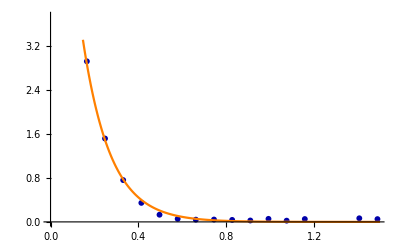

```mathematica
Clear[f]
f[r_]:=10.698201438598309 ⅇ^(-7.941329322829148 r)
Show[ListPlot[morseFitScatter,PlotMarkers->{Automatic,6},PlotStyle->Darker[Blue]],Plot[f[x],{x,0.001,1.5},PlotStyle->{Orange},AxesLabel ->{Distance,Energy}]]
```

```mathematica
f[r]//FortranForm
```

10.698201438598309/E**(7.941329322829148*r)

## Fit of the entropy for angle 7 (python convention), angle 8 (mathematica convention) Kernel Smoother

```mathematica
start=startingDistance[[8]]+9;
scatter=Table[{distances[[i]],entropy[[8,i]]},{i,start,Length[distances]-start}];
```

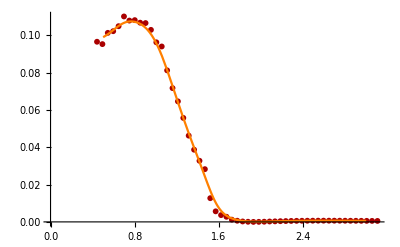

```mathematica
Clear[f]
k[x_,y_,σ_]:=Exp[-(x-y)^2/(2 σ^2)]
σ=0.083;
every=3;
s=scatter[[;;;;every]];
f[r_]:=(∑_(i=1)^Length[s] k[r,s⟦i,1⟧,σ] s⟦i,2⟧)/(∑_(i=1)^Length[s] k[r,s⟦i,1⟧,σ])
Show[ListPlot[s,PlotMarkers->{Automatic,6},PlotStyle->Darker[Red]],Plot[f[x],{x,0.5,3.0},PlotStyle->{Orange},AxesLabel ->{Distance,Energy}]]
```